Warning: more than 31 qubits may cause errors - MMA uses ints to store array lengths

```mathematica
SetDirectory @ NotebookDirectory[];
```

```mathematica
CreateQureg[numQb_] :=
	{
		numQb, 
		0, 
		Prepend[ConstantArray[0.0, 2^numQb-1], 1],
		ConstantArray[0.0, 2^numQb]
	}
	
CreateDensityQureg[numQb_] :=
	{
		numQb, 
		1, 
		Prepend[ConstantArray[0.0, 2^(2numQb)-1], 1],
		ConstantArray[0.0, 2^(2numQb)]
	}
	
ToWavefunc[qureg_List] :=
	With[
		{mixed = MapThread[#1 + ⅈ #2 &, {qureg[[3]], qureg[[4]]}]},
		If[
			qureg[[2]] == 0,
			mixed,
			Transpose @ ArrayReshape[mixed, {2^qureg[[1]],2^qureg[[1]]}]
		]
	]
```

```mathematica
link = Install["quest_link"];
LinkPatterns[link] // TableForm
```

ApplyCircuitInner[opcodes_List,ctrls_List,targs_List,params_List,qureg_List]
CalcProbOfOutcome[qureg_List,qb_Integer,outcome_Integer]
CalcFidelity[qureg1_List,qureg2_List]
InitZeroState[qureg_List]
InitPlusState[qureg_List]
InitClassicalState[qureg_List,state_Integer]
InitPureState[targetQureg_List,pureQureg_List]
ApplyOneQubitDepolariseError[qureg_List,qb_Integer,prob_Real]
ApplyTwoQubitDepolariseError[qureg_List,qb1_Integer,qb2_Integer,prob_Real]
ApplyOneQubitDephaseError[qureg_List,qb_Integer,prob_Real]
ApplyTwoQubitDephaseError[qureg_List,qb1_Integer,qb2_Integer,prob_Real]

```mathematica
mytest = ApplyOneQubitDephaseError[CreateQureg[4],0, .3]
```

Error:  Incorrect use of function applyOneQubitDephaseError: Operation valid only for density matrices.

Error:  The QuEST link must now be killed.

$Failed

```mathematica
mytest
```

$Aborted

```mathematica
mytest = 
Table[
	ApplyOneQubitDephaseError[CreateQureg[4],0, .3],
	{t,1,20}
]
```

Error:  Incorrect use of function applyOneQubitDephaseError: Operation valid only for density matrices.

Error:  The QuEST link must now be killed.

LinkObject::linkd: Unable to communicate with closed link LinkObject['/Users/tysonjones/Desktop/MMAQuEST/QuEST-MMA/quest_link',4030,19].

LinkObject::linkn: Argument LinkObject['/Users/tysonjones/Desktop/MMAQuEST/QuEST-MMA/quest_link',4030,19] in LinkWrite[LinkObject['/Users/tysonjones/Desktop/MMAQuEST/QuEST-MMA/quest_link',4030,19],CallPacket[9,{{4,0,{1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}},0,0.3}]] has an invalid LinkObject number; the link may be closed.

General::stop: Further output of LinkObject::linkn will be suppressed during this calculation.

{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}

```mathematica
mytest
```

```mathematica
FullForm[mytest]
```

Null

```mathematica
Echo[123]; 5
```

123

5

```mathematica
x =Block[{Echo[123]}; 5]
```

Block::argr: Block called with 1 argument; 2 arguments are expected.

Block[{Echo[123]};5]

```mathematica
qureg = CreateDensityQureg[10];
```

```mathematica
probs = Table[
	CalcProbOfOutcome[
		ApplyTwoQubitDepolariseError[qureg, 0, 1, prob],
		0, 0],
	{prob, 0, .75, .01}
];
```

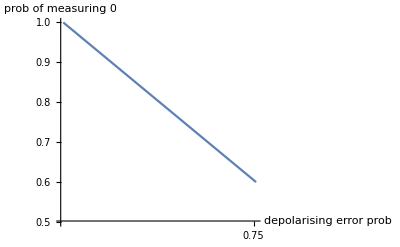

```mathematica
ListLinePlot[
	probs,
	AxesLabel-> {"depolarising error prob", "prob of measuring 0"},
	Ticks -> {{{75,.75}},Automatic},
	PlotRange-> {All,{.5,1}}
]
```

```mathematica
Uninstall[link]
Uninstall["quest_link"]
```

LinkObject::linkn: Argument LinkObject['/Users/tysonjones/Desktop/MMAQuEST/QuEST-MMA/quest_link',258,11] in LinkClose[LinkObject['/Users/tysonjones/Desktop/MMAQuEST/QuEST-MMA/quest_link',258,11]] has an invalid LinkObject number; the link may be closed.

'/Users/tysonjones/Desktop/MMAQuEST/QuEST-MMA/quest_link'

LinkObject::linkn: Argument LinkObject['/Users/tysonjones/Desktop/MMAQuEST/QuEST-MMA/quest_link',258,11] in LinkClose[LinkObject['/Users/tysonjones/Desktop/MMAQuEST/QuEST-MMA/quest_link',258,11]] has an invalid LinkObject number; the link may be closed.

Unset::norep: Assignment on LinkPatterns for LinkPatterns[LinkObject['/Users/tysonjones/Desktop/MMAQuEST/QuEST-MMA/quest_link',258,11]] not found.

quest_link

## Circuit specification

```mathematica
(* disables gate (symbol and integer suscript) commutivity, replaces Times with Dot *)
$Pre = 
  Function[{arg}, 
   ReleaseHold[
    Hold[arg] //.  
     Times[α___, 
       patt : (Longest[(Subscript[_Symbol, _Integer]|Subscript[_Symbol, _Integer][___]) ..]), ω___] :> 
      Times[α, Dot[patt], ω]], HoldAll];
```

```mathematica
(* opcodes *)
getOpCode[gate_] :=
	gate /. {H->0,X->1,Y->2,Z->3,Rx->4,Ry->5,Rz->6,S->7,T->8}

(* recognising gates *)
gatePatterns = {
	Subscript[C, ctrl_Integer][Subscript[gate_Symbol, targ__Integer][arg_]] :> {getOpCode[gate], ctrl, targ, arg},
	Subscript[C, ctrl_Integer][Subscript[gate_Symbol, targ_Integer]] :> {getOpCode[gate], ctrl, targ, 0},
	Subscript[gate_Symbol, targ_Integer][arg_] :> {getOpCode[gate], -1, targ, arg},
	Subscript[gate_Symbol, targ_Integer] :> {getOpCode[gate], -1, targ, 0}
};

(* converting gate sequence to code lists: {opcodes, ctrls, targs, params} *)
codifyCircuit[circuit_Dot] :=
	circuit /. Dot -> List /. gatePatterns // Transpose
```

```mathematica
ApplyCircuit[circuit_Dot, qureg_List] :=
	With[
		{codes = codifyCircuit[circuit]},
		ApplyCircuitInner[codes[[1]], codes[[2]], codes[[3]], codes[[4]], qureg]
	]
```

```mathematica
u[θ_] := Subscript[H, 0] Subscript[T, 1] Subscript[C, 0][Subscript[S, 2]] Subscript[Z, 3] Subscript[Ry, 3][θ] Subscript[C, 3][Subscript[Rz, 2][θ]] Subscript[H, 0] Subscript[T, 1] Subscript[C, 0][Subscript[S, 2]] Subscript[Z, 3] Subscript[Ry, 3][θ] Subscript[C, 3][Subscript[Rz, 2][θ]] Subscript[H, 0] Subscript[T, 1] Subscript[C, 0][Subscript[S, 2]] Subscript[Z, 3] Subscript[Ry, 3][θ] Subscript[C, 3][Subscript[Rz, 2][θ]]
ψ = InitPlusState @ CreateQureg[15];

ListPlot @  Table[
	CalcFidelity[ψ, ApplyCircuit[u[θ],ψ]],
	{θ, 0, 2π, .05}
]
```

LinkObject::linkw: Unable to write data to closed link ….

-Graphics-

```mathematica
Print["hello there"]
```

hello there

## Qureg format

{ numQb, isDensityMatrix, realAmps, complexAmps }

```mathematica
createQureg[3];
toWavefunc @ % // MatrixForm
```

(1.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.+0. ⅈ)

```mathematica
createDensityQureg[3];
toWavefunc @ %// MatrixForm
```

(1.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ)